```mathematica
K0[ajp_,aj_,Γ_]:=KroneckerDelta[ajp,0] KroneckerDelta[aj,0] + Sqrt[1-Γ](KroneckerDelta[aj,ajp] -KroneckerDelta[ajp,0] KroneckerDelta[aj,0])
Ki[ajp_,aj_,i_,Γ_]:=Sqrt[Γ] KroneckerDelta[ajp,i-1] KroneckerDelta[aj,i]
SigmaTau[a1_,b1_,b2_,σ_]:= KroneckerDelta[σ,1]KroneckerDelta[a1,b1]+(1-KroneckerDelta[σ,1])KroneckerDelta[a1,b2]
wg[c_,τ_,q_]:= KroneckerDelta[c,τ]/(q^2-1) -(1- KroneckerDelta[c,τ])/(q(q^2-1))
```

```mathematica
K0K0dag[ajp_,aj_,bjp_,bj_,Γ_]:=K0[ajp,aj,Γ]*K0[bj,bjp,Γ]
KiKidag[ajp_,aj_,bjp_,bj_,i_,Γ_]:=Ki[ajp,aj,i,Γ]*Ki[bjp,bj,i,Γ]
```

```mathematica
wd[σ_,τ_,q_,Γ_,p_]:=Sum[(K0K0dag[a0p,a0,b0p,b0,Γ]+Sum[KiKidag[a0p,a0,b0p,b0,i,Γ],{i,0,q-1}])*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*(K0K0dag[a1p,a1,b1p,b1,Γ]+Sum[KiKidag[a1p,a1,b1p,b1,i,Γ],{i,0,q-1}])*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ]((1-p)^2 + p^2 *KroneckerDelta[b0p,a1p]KroneckerDelta[b0p,a0p]KroneckerDelta[b1p,a0p]KroneckerDelta[b1p,a1p]),{a1,0,q-1},{a1p,0,q-1},{b1,0,q-1},{b1p,0,q-1},{a0,0,q-1},{a0p,0,q-1},{b0,0,q-1},{b0p,0,q-1},Assumptions->{p>0,q>0,Element[q,Integers]}]
w3[a_,b_,c_,q_,Γ_,p_]:=wd[a,1,q,Γ,p] wd[b,1,q,Γ,p]wg[c,1,q^2]+wd[a,-1,q,Γ,p] wd[b,-1,q,Γ,p]wg[c,-1,q^2]
```

```mathematica
wdtest[σ_,τ_,q_,Γ_,p_]:=
Which [σ==1&&τ==1,(1/2*q(1+q)+Γ^2) 2p^2-2q^2  p + q^2,
σ==-1&&τ==-1,(1-p)^2(1+2(q-1)(1-Γ)+(q-1)(q-2)(1-Γ)^2+(q-1)((1-Γ)^2+Γ^2) )+p^2(1+(q-1)((1-Γ)^2+Γ^2)),
σ==-1 &&τ==1,(1-2p+2p^2)(2Γ^2+q),
σ==1&&τ==-1, q-2q p + p^2(2q-2(q-1)(Γ-Γ^2))
]
w3test[a_,b_,c_,q_,Γ_,p_]:=wdtest[a,1,q,Γ,p] wdtest[b,1,q,Γ,p]wg[c,1,q^2]+wdtest[a,-1,q,Γ,p] wdtest[b,-1,q,Γ,p]wg[c,-1,q^2]
```

```mathematica
testFun[σ_,τ_,p_,q_,Γ_]:= Sum[K0K0dag[a0p,a0,b0p,b0,Γ]*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*Sum[KiKidag[a1p,a1,b1p,b1,i,Γ],{i,0,q-1}]*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ],{a1,0,q-1},{a1p,0,q-1},{b1,0,q-1},{b1p,0,q-1},{a0,0,q-1},{a0p,0,q-1},{b0,0,q-1},{b0p,0,q-1},Assumptions->{q>0,Element[q,Integers]}]
(*testFun[σ_,τ_,p_,q_,Γ_]:= Sum[K0K0dag[a0p,a0,b0p,b0,Γ]*SigmaTau[a0p,b0p,b1p,σ]*SigmaTau[a0,b0,b1,τ]*K0K0dag[a1p,a1,b1p,b1,Γ]*SigmaTau[a1p,b1p,b0p,σ]*SigmaTau[a1,b1,b0,τ],{a1,0,q-1},{a1p,0,q-1},{b1,0,q-1},{b1p,0,q-1},{a0,0,q-1},{a0p,0,q-1},{b0,0,q-1},{b0p,0,q-1},Assumptions->{q>0,Element[q,Integers]}]*)
```

```mathematica
testFun[-1,-1,p,3,Γ]
testFun[-1,1,p,3,Γ]
testFun[1,-1,p,3,Γ]
testFun[1,1,p,3,Γ]
```

0

Γ+(1-Γ) Γ

2 (1-Γ) Γ

2 Γ+4 (1-Γ) Γ

```mathematica
wdtest[-1,-1,2,Γ,p]
```

p^2 (1+(1-Γ)^2+Γ^2)+(1-p)^2 (1+2 (1-Γ)+(1-Γ)^2+Γ^2)

```mathematica
Simplify[wd[-1,-1,3,Γ,p]]
Simplify[wd[-1,1,3,Γ,p]]
Simplify[wd[1,-1,3,Γ,p]]
FullSimplify[wd[1,1,3,Γ,p]]
```

9-12 Γ+6 Γ^2-6 p (3-4 Γ+2 Γ^2)+2 p^2 (6-8 Γ+5 Γ^2)

(1-2 p+2 p^2) (3+2 Γ^2)

3-6 p+p^2 (6-4 Γ+4 Γ^2)

9+2 p (-9+p (6+Γ^2))

```mathematica
Simplify[(1-p)^2(1+2(q-1)(1-Γ)+(1-Γ)^2(q-1)^2 + 2(q-1)Γ +2(q-1)^2Γ(1-Γ)+(q-1)^2 Γ^2)+p^2(1+(q-1)(1-Γ)^2+ Γ^2(q-1) +  2Γ)]
```

q^2-2 p q^2+p^2 (q^2-2 (-2+Γ) Γ+q (1-2 Γ+2 Γ^2))

```mathematica
Simplify[4-8 p+p^2 (4-2 (-2+Γ) Γ+2 (1-2 Γ+2 Γ^2))]
```

4-8 p+2 p^2 (3+Γ^2)

```mathematica
2^17
```

131072

```mathematica
Simplify[wdtest[1,1,3,Γ,p]]
Simplify[wdtest[1,-1,3,Γ,p]]
Simplify[wdtest[-1,1,3,Γ,p]]
FullSimplify[wdtest[-1,-1,3,Γ,p]]
```

9-18 p+2 p^2 (6+Γ^2)

3-6 p+p^2 (6-4 Γ+4 Γ^2)

(1-2 p+2 p^2) (3+2 Γ^2)

9+6 (-2+Γ) Γ-6 p (3+2 (-2+Γ) Γ)+2 p^2 (6+Γ (-8+5 Γ))

```mathematica
Collect[Simplify[wdtest[1,1,q,Γ,p]],q]
Collect[Simplify[wdtest[1,-1,q,Γ,p]],q]
Collect[Simplify[wdtest[-1,1,q,Γ,p]],q]
Collect[Simplify[wdtest[-1,-1,q,Γ,p]],q]
```

p^2 q+(1-2 p+p^2) q^2+2 p^2 Γ^2

2 p^2 (1-Γ) Γ+q (1-2 p+2 p^2+2 p^2 (-1+Γ) Γ)

(1-2 p+2 p^2) q+2 (1-2 p+2 p^2) Γ^2

(-1+p)^2 q^2 (-1+Γ)^2+2 p^2 Γ-2 p^2 Γ^2+q (-(-1+p)^2 (-2+Γ) Γ+p^2 (1-2 Γ+2 Γ^2))

```mathematica
testFun[-1,-1,p,4,Γ]
testFun[1,-1,p,4,Γ]
testFun[1,1,p,4,Γ]
```

0

3 (1-Γ) Γ

3 Γ+9 (1-Γ) Γ

```mathematica
w110/.{Γ->0,q->2}
```

-1/60 (4 (1-p)^2+2 p^2)^2+4/15 (1-2 p+2 p^2)^2

```mathematica
w000=w3test[1,1,1,q,Γ,p];
w001=w3test[1,1,-1,q,Γ,p];
w010=w3test[1,-1,1,q,Γ,p];
w100=w3test[-1,1,1,q,Γ,p];
w101=w3test[-1,1,-1,q,Γ,p];
w011=w3test[1,-1,-1,q,Γ,p];
w110=w3test[-1,-1,1,q,Γ,p];
w111=w3test[-1,-1,-1,q,Γ,p];
```

## Thermodynamic limit

```mathematica
n=100;
minFA1=Min[-(2n+1)Log[w110]-Log[w010]-Log[w100]-(2n+1)Log[w000],-n Log[w001]-(n+1)Log[w111]-(n+2)(Log[w010]+Log[w100])+2(n+1)Log[w000] -(2n+1)Log[w000]];
minFAB =Min[-(2n+2)(Log[w110]+Log[w111]+Log[w010]+Log[w100]-2Log[w000]),-(4n+4)(Log[w110]+2Log[w000])];
Fempty1=-(4n+4)Log[w000];
minFA2=Min[-(2n+1)Log[w110]-Log[w010]-Log[w100]-(2n+1)Log[w000],-(n+1) Log[w001]-(n+2)(Log[w010]+Log[w100])-n Log[w111]-(2n+1)Log[w000] ];
minFA3=Min[-2n Log[w110]-Log[w010]-Log[w100]-2n Log[w000],-n Log[w001]-n Log[w111]-(n+1)(Log[w010]+Log[w100])-2n Log[w000] ];
minFAB3 =Min[-(2n+1)(Log[w110]+Log[w111]+Log[w010]+Log[w100]),-(4n+2)(Log[w110]+2Log[w000])];
Fempty3=-(4n+2)Log[w000];
```

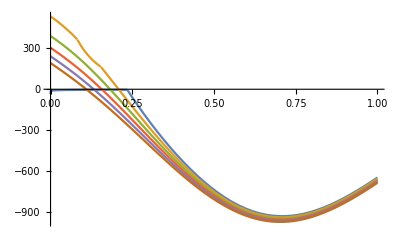

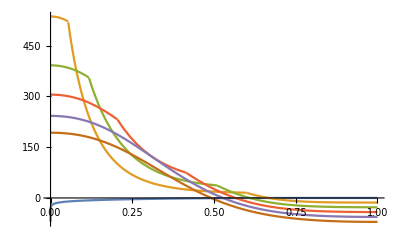

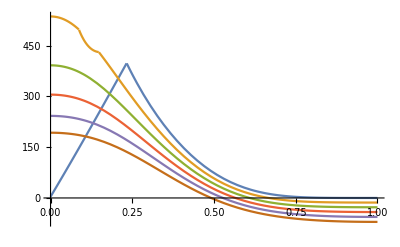

```mathematica
Plot[Evaluate[Table[{2minFA1-minFAB-Fempty1}/.{q->2,Γ->0.001*g},{g,0,100,20}]],
{p,0,1}]
Plot[Evaluate[Table[{2minFA2-minFAB-Fempty1}/.{q->2,Γ->0.001*g},{g,0,100,20}]],
{p,0,1}]
Plot[Evaluate[Table[{2minFA3-minFAB3-Fempty3}/.{q->2,Γ->0.001*g},{g,0,100,20}]],
{p,0,1}]
```

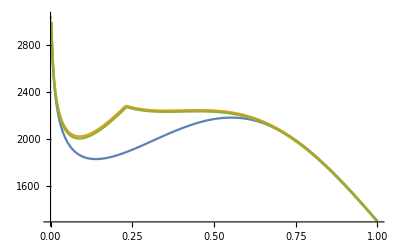

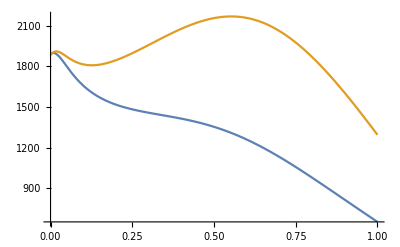

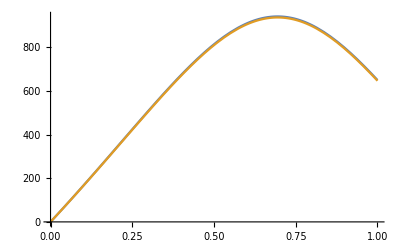

```mathematica
Plot[Evaluate[{2minFA1,2minFA2,2minFA3}/.{q->2,Γ->0.001}],
{p,0,1}]
Plot[Evaluate[{minFAB,minFAB3}/.{q->2,Γ->0.001}],
{p,0,1}]
Plot[Evaluate[{Fempty1,Fempty3}/.{q->2,Γ->0.001}],
{p,0,1}]
```

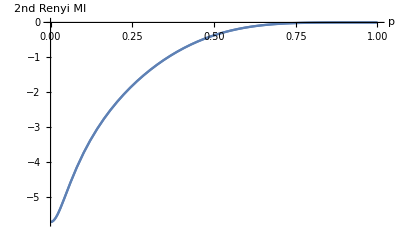

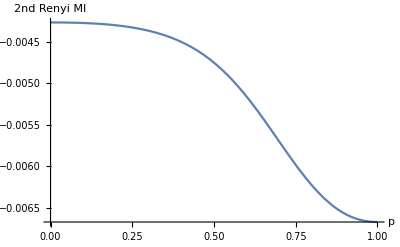

```mathematica
Plot[{-Log[w100*w010/(w110*w000)],-Log[w100*w010/(w110*w111)]}/.{q->2,Γ->0.001},
{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22}]
Plot[-2Log[w000/w111]/.{q->2,Γ->0.001},
{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22}]
```

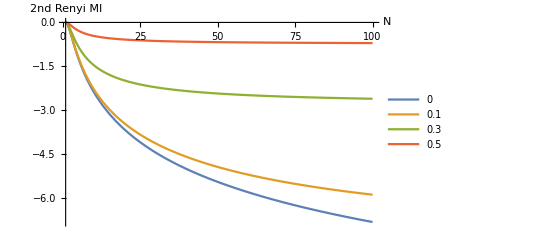

```mathematica
renyiMI2N = Plot[{-2Log[w100*w010/(w110*w000)]/.{q->2,p->0,Γ->(1/n)},-2Log[w100*w010/(w110*w000)]/.{q->2,p->.1,Γ->(1/n)},
-2Log[w100*w010/(w110*w000)]/.{q->2,p->.3,Γ->(1/n)},
-2Log[w100*w010/(w110*w000)]/.{q->2,p->.5,Γ->(1/n)}},{n,1,100},AxesLabel->{"N","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->{0,0.1,0.3,0.5}]
Export["/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2N.png",Rasterize[renyiMI2N,ImageResolution->150]];
```

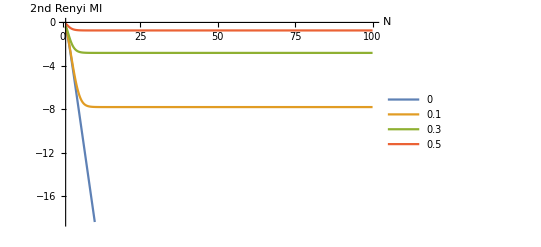

```mathematica
Plot[{-2Log[w100*w010/(w110*w000)]/.{q->2,p->0,Γ->(Exp[-n])},-2Log[w100*w010/(w110*w000)]/.{q->2,p->.1,Γ->(Exp[-n])},
-2Log[w100*w010/(w110*w000)]/.{q->2,p->.3,Γ->(Exp[-n])},
-2Log[w100*w010/(w110*w000)]/.{q->2,p->.5,Γ->(Exp[-n])}},{n,1,100},AxesLabel->{"N","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->{0,0.1,0.3,0.5}]
```

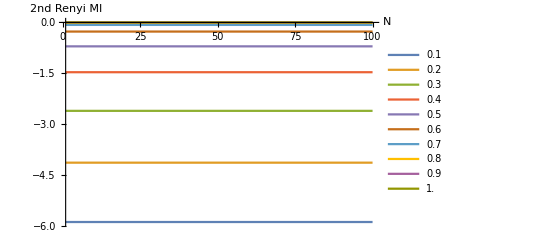

```mathematica
Plot[Evaluate@(Table[-2Log[w100*w010/(w110*w000)]/.{q->2,p->.1*g,Γ->(1/n)},{g,1,10,1}]),{n,1,100},AxesLabel->{"N","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.1*g,{g,1,10,1}],Spacings->0.15]]
```

```mathematica
Clear[p,Γ,q]
(w000)/.{q->2,p->0,Γ->0}
```

1

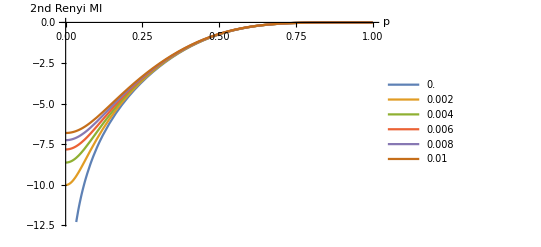

/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2_area.png

```mathematica
renyiMI2 = Plot[Evaluate[Table[-2Log[w100*w010/(w110* w000)]/.{q->2,Γ->.0001*g},{g,0,100,20}]],{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.0001*g,{g,0,100,20}],Spacings->0.15],PlotRange->Automatic]
Export["/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2_area.png",Rasterize[renyiMI2,ImageResolution->150]]
```

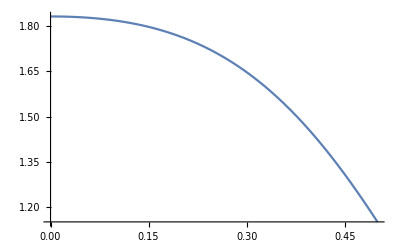

-((q-2 p q+2 p^2 q)^2)/(q^2 (-1+q^4))+((q^2-2 p q^2+p^2 q (1+q))^2)/(-1+q^4)

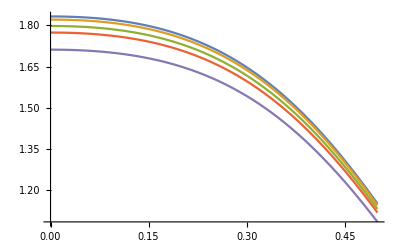

```mathematica
Plot[-Log[(w101*w010/(w111*w000))]/.{q->2,Γ->0},{p,0,0.5}]
Clear[q]
w000/.{Γ->0}
Plot[{-Log[(w101*w010/(w111*w000))]/.{q->2,Γ->0},
-Log[(w101*w010/(w111*w000))]/.{q->2,Γ->0.01},
-Log[(w101*w010/(w111*w000))]/.{q->2,Γ->0.03},
-Log[(w101*w010/(w111*w000))]/.{q->2,Γ->0.05},
-Log[(w101*w010/(w111*w000))]/.{q->2,Γ->0.1}},{p,0,0.5}]
```

-((q-2 p q+2 p^2 q)^2)/(q^2 (-1+q^4))+((q^2-2 p q^2+p^2 q (1+q))^2)/(-1+q^4)

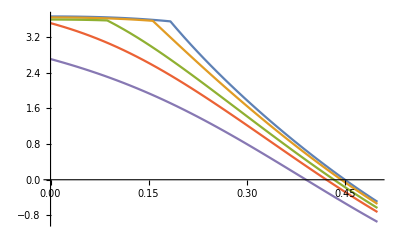

```mathematica
Clear[q,MaTex]
w000/.{Γ->0}
Plot[{Min[-Log[w110/w111/w000],-2Log[w101*w010/w111/w000]]/.{q->2,Γ->0},
Min[-Log[w110/w111/w000],-2Log[w101*w010/w111/w000]]/.{q->2,Γ->0.01},
Min[-Log[w110/w111/w000],-2Log[w101*w010/w111/w000]]/.{q->2,Γ->0.03},
Min[-Log[w110/w111/w000],-2Log[w101*w010/w111/w000]]/.{q->2,Γ->0.05},
Min[-Log[w110/w111/w000],-2Log[w101*w010/w111/w000]]/.{q->2,Γ->0.1}}
,{p,0,0.5}, PlotLegends->LineLegend[Automatic,{0,0.01,0.03,0.05,0.1},Spacings->0.15,LegendLabel->MaTeX["\\Gamma",Magnification->2]],AxesLabel->{MaTeX["p",Magnification->2],MaTeX["c(p,\\Gamma)",Magnification->2]},LabelStyle->{FontSize->22}]
```

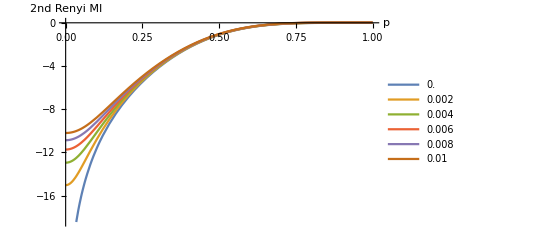

```mathematica
Plot[Evaluate@Table[(-3 Log[w010*w100/w110]-Log[w111]+4Log[w000])/.{q->2,Γ->.0001*g},{g,0,100,20}],{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.0001*g,{g,0,100,20}],Spacings->0.15]]
```

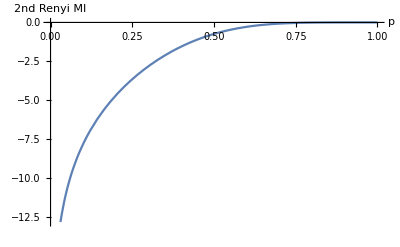

```mathematica
Plot[-2Log[w100*w010/(w110* w000)]/.{q->2,Γ->0},{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.0001*g,{g,0,100,20}],Spacings->0.15]]
```

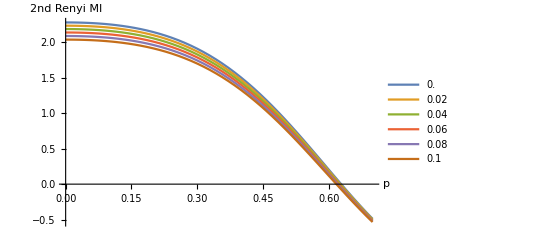

```mathematica
Plot[Evaluate@Table[-2Log[2w010*w101/(w111* w000)]/.{q->2,Γ->.01*g},{g,0,10,2}],{p,0,0.7},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.01*g,{g,0,10,2}],Spacings->0.15]]
```

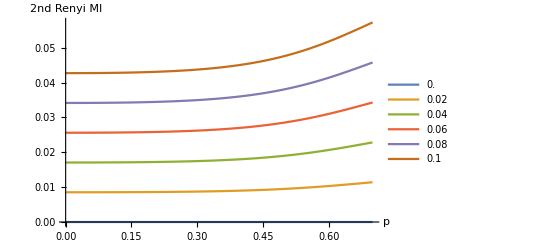

```mathematica
Plot[Evaluate@Table[2Log[w000/ w111]/.{q->2,Γ->.001*g},{g,0,10,2}],{p,0,0.7},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->LineLegend[Automatic,Table[.01*g,{g,0,10,2}],Spacings->0.15]]
```

32

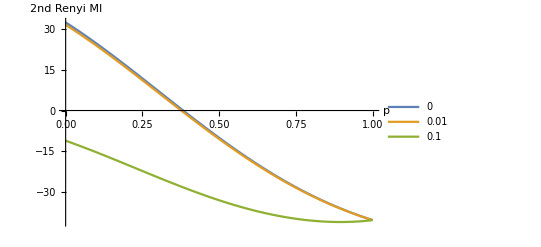

```mathematica
n=32
renyiVol = Plot[{-2n Log[2w100*w011/(w111*w000)]-2Log[Binomial[n,n/2]]/.{q->2,p->0},
-2n Log[2w100*w011/(w111*w000)]-2Log[Binomial[n,n/2]]/.{q->2,p->0.1},
-2n Log[2w100*w011/(w111*w000)]-2Log[Binomial[n,n/2]]/.{q->2,p->0.5}},{Γ,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->{0,0.01,0.1}]
```

32

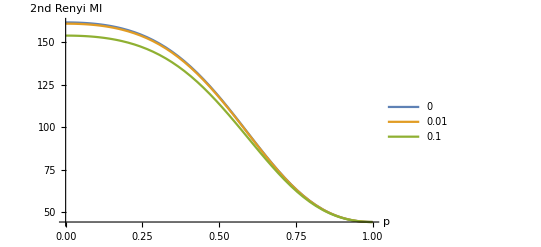

/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2_volume.png

```mathematica
n=32
renyiVol = Plot[{-2n Log[w100*w011/(2w111*w000) ]/.{q->2,Γ->0},
-2n Log[w100*w011/(2w111*w000)]/.{q->2,Γ->0.01},
-2n Log[w100*w011/(2w111*w000)]/.{q->2,Γ->0.1}},{p,0,1},AxesLabel->{"p","2nd Renyi MI"},LabelStyle->{FontSize->22},PlotLegends->{0,0.01,0.1}]
Export["/Users/cathy/Google Drive/Random circuits/Pics/renyiMI2_volume.png",Rasterize[renyiVol,ImageResolution->150]]
```

```mathematica
W000[p_,q_,Γ_]:=w3test[1,1,1,q,Γ,p];
W001[p_,q_,Γ_]:=w3test[1,1,-1,q,Γ,p];
W010[p_,q_,Γ_]:=w3test[1,-1,1,q,Γ,p];
W100[p_,q_,Γ_]:=w3test[-1,1,1,q,Γ,p];
W101[p_,q_,Γ_]:=w3test[-1,1,-1,q,Γ,p];
W011[p_,q_,Γ_]:=w3test[1,-1,-1,q,Γ,p];
W110[p_,q_,Γ_]:=w3test[-1,-1,1,q,Γ,p];
W111[p_,q_,Γ_]:=w3test[-1,-1,-1,q,Γ,p];
```

## The mixed boundary condition

```mathematica
FHalfUpDown[n_]:=-(n-1)(Log[w010*w011]-(n/2-1)(n-1)Log[(w000*w111)]-Log[Binomial[n,n/2]])
FHalfMostUp[n_]:=(-(7/8n^2-7n/4)Log[w000]-(n^2/8-n/4)Log[w111]-n Log[w101])
FHalfMostDown[n_]:=(-(7/8n^2-7n/4)Log[w111]-(n^2/8-n/4)Log[w000]-n Log[ w100])
FHalfUpHDomWall[n_]:=(-(n(n-1)-n/2-1)Log[w000]-(n/2-1)Log[w110]-Log[w010]-Log[w100])
FHalfDownHDomWall[n_]:=(-(n(n-1)-n/2-1)Log[w111]-(n/2-1)Log[w001]-Log[w101]-Log[w011])
(*MinValue[{FHalfUpDown[n]/.{q->2,Γ->0.01}||FHalfMostUp[n]/.{q->2,Γ->0.01}||FHalfMostDown[n]/.{q->2,Γ->0.01},p>0},p]*)
FHalf1[n_,p_,q_,Γ_]:=(-(n/2-1)(n-1)Log[(W000[p,q,Γ]*W111[p,q,Γ])]-(n-1)(Log[W010[p,q,Γ]*W011[p,q,Γ]])-Log[Binomial[n,n/2]])
FHalf2[n_,p_,q_,Γ_]:=(-(7/8n^2-7n/4)Log[W000[p,q,Γ]]-(n^2/8-n/4)Log[W111[p,q,Γ]]-n Log[W101[p,q,Γ]])
FHalf3[n_,p_,q_,Γ_]:=(-(7/8n^2-7n/4)Log[W111[p,q,Γ]]-(n^2/8-n/4)Log[W000[p,q,Γ]]-n Log[ W100[p,q,Γ]])
FHalf4[n_,p_,q_,Γ_]:=(-(n(n-1)-n/2-1)Log[W000[p,q,Γ]]-(n/2-1)Log[W110[p,q,Γ]]-Log[W010[p,q,Γ]]-Log[W100[p,q,Γ]])
FHalf5[n_,p_,q_,Γ_]:=(-(n(n-1)-n/2-1)Log[W111[p,q,Γ]]-(n/2-1)Log[W001[p,q,Γ]]-Log[W101[p,q,Γ]]-Log[W011[p,q,Γ]])
FABMin [n_,p_,q_,Γ_]:= Min[FHalf1[n,p,q,Γ],FHalf2[n,p,q,Γ], FHalf3[n,p,q,Γ],FHalf4[n,p,q,Γ],FHalf5[n,p,q,Γ]]
```

## The all down boundary condition

```mathematica
FDownAll[n_,p_,q_,Γ_]:=-n^2 Log[W111[p,q,Γ]]
FDownMostDown[n_,p_,q_,Γ_]:=(-n(n-1)/2Log[W111[p,q,Γ]]-(n-2)(n-3)/2Log[W000[p,q,Γ]]-2(n-2)Log[W010[p,q,Γ]]-2Log[W110[p,q,Γ]]- Log[n])
FDownH[n_,p_,q_,Γ_]:=(-(n^2-2n)Log[W000[p,q,Γ]]-n Log[W110[p,q,Γ]])
FDownMin [n_,p_,q_,Γ_]:= Min[FDownAll[n,p,q,Γ], FDownMostDown[n,p,q,Γ],FDownH[n,p,q,Γ]]
```

## The all up boundary condition

```mathematica
FUpAll[n_,p_,q_,Γ_]:=-n^2 Log[W000[p,q,Γ]]
FUpMostUp[n_,p_,q_,Γ_]:=-n(n-1)/2Log[W000[p,q,Γ]]-(n-2)(n-3)/2Log[W111[p,q,Γ]]-2(n-2)Log[W011[p,q,Γ]]-2Log[W001[p,q,Γ]]- Log[n]
FUpH[n_,p_,q_,Γ_]:=-(n^2-2n)Log[W111[p,q,Γ]]-n Log[W001[p,q,Γ]]
FUpMin [n_,p_,q_,Γ_]:= Min[FUpAll[n,p,q,Γ],FUpMostUp[ n,p,q,Γ],FUpH[n,p,q,Γ]]
```

32

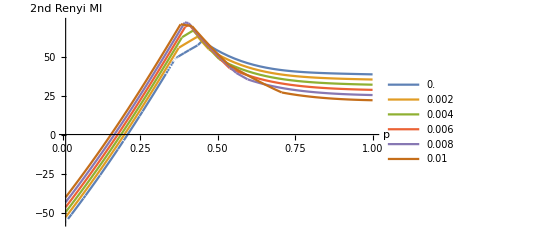

```mathematica
n=32
q=2;
Plot[Evaluate[Table[-(2 FABMin [n,p,q,g*0.001]-FDownMin[n,p,q,g*0.001]-FUpMin[n,p,q,g*0.001]),{g,0,10,2}]],{p,0.01,1},AxesLabel->{"p","2nd Renyi MI"},PlotLegends->LineLegend[Automatic,Table[g*0.001,{g,0,10,2}]],LabelStyle->{FontSize->22}]
```

```mathematica
1
```

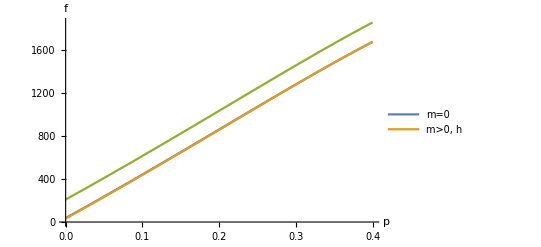

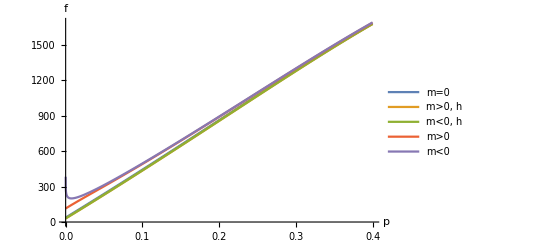

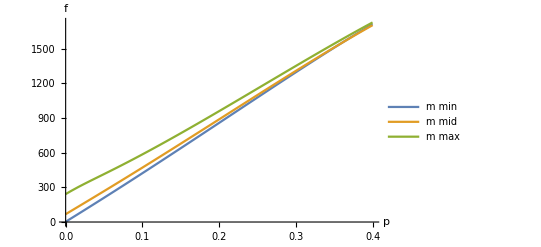

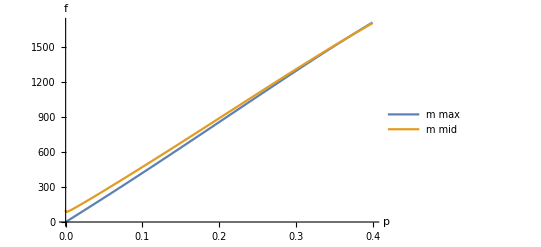

```mathematica
n=32;
q=2;
Γ=0.001;
Plot[Evaluate[{FHalf1[n,p,q,0],FHalf2[n,p,q,0.01],FHalf3[n,p,q,0.1]}],{p,0,0.4},AxesLabel->{"p","f"},PlotLegends->{"m=0","m>0, h"},LabelStyle->{FontSize->22}]
Plot[Evaluate[{FHalf1[n,p,q,Γ],FHalf2[n,p,q,Γ],FHalf3[n,p,q,Γ],FHalf4[n,p,q,Γ],FHalf5[n,p,q,Γ]}],{p,0,0.4},AxesLabel->{"p","f"},PlotLegends->{"m=0","m>0, h","m<0, h","m>0","m<0"},LabelStyle->{FontSize->22}]
Plot[Evaluate[{FDownAll[n,p,q,Γ],FDownMostDown[n,p,q,Γ],FDownH[n,p,q,Γ]}],{p,0,0.4},AxesLabel->{"p","f"},PlotLegends->{"m min","m mid","m max"},LabelStyle->{FontSize->22}]
Plot[Evaluate[{FUpAll[n,p,q,Γ],FUpMostUp[n,p,q,Γ]}],{p,0,0.4},AxesLabel->{"p","f"},PlotLegends->{"m max","m mid","m min"},LabelStyle->{FontSize->22}]
```

```mathematica
FAhalf1[n_]:=(2((n^2/2-n)(-Log[w000]-Log[w111])+n(-Log[w010]+-Log[w011]))-2n Log[2]-(-n(n-1)/2 Log[w111]-(n-1)(n-2)/2Log[ w001]-2(n-1)Log[w010]-Log[w001]-n Log[2] )-n^2Log[w000])/n^2
FAhalf1[n_]:=(2((n^2/2-n)(-Log[w000]-Log[w111])+n(-Log[w010]+-Log[w011]))-2n Log[2]-(-n(n-1)/2 Log[w111]-(n-1)(n-2)/2Log[ w001]-2(n-1)Log[w010]-Log[w001]-n Log[2] )-n^2Log[w000])/n^2

FAhalf[n_]:=MinValue[a x^2+b x+c,x]

FAm1[n_]:=(2(-(n^2/8-n/4)Log[w111]-n/2Log[ w100]-(7/8n^2-3n/4)Log[w000])+(n(n-1)/2Log[w111]+(n-1)(n-2)/2Log[ w000]+2(n-1)Log[w011]+Log[w001]+n Log[2]))/n^2
FAmm1[n_]:=(2(-(n^2/8-n/4)Log[w000]-n/2Log[ w101]-(7/8n^2-3n/4)Log[w111])+(n(n-1)/2Log[w111]+(n-1)(n-2)/2 Log[w000]+2(n-1)Log[w011]+Log[w001]+n Log[2]))/n^2
```

30

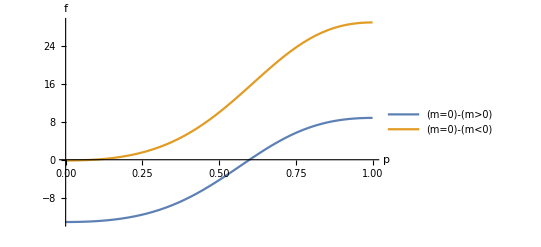

```mathematica
n=30
Plot[Evaluate[{-FHalfUpDown[n] + FHalfMostUp[n],-FHalfUpDown[n] + FHalfMostDown[n]}/.{q->2,Γ->0.01}],{p,0,1},AxesLabel->{"p","f"},PlotLegends->{"(m=0)-(m>0)","(m=0)-(m<0)"},LabelStyle->{FontSize->22}]
```

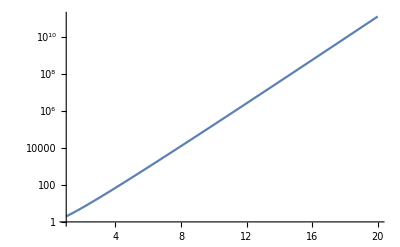

```mathematica
LogPlot[Binomial[2n,n],{n,1,20}]
```

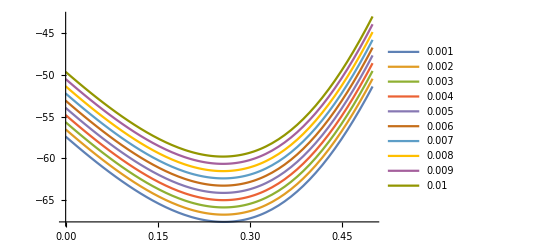

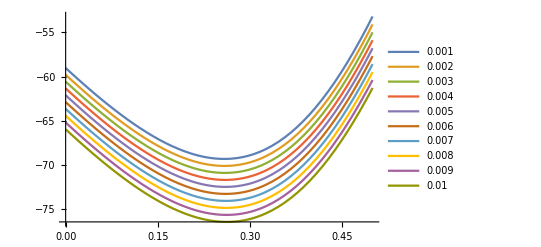

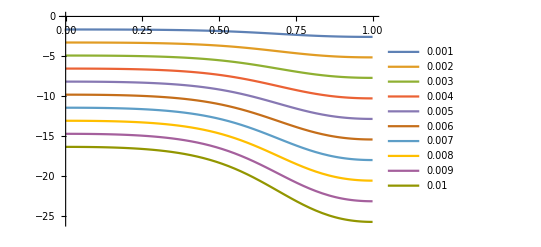

```mathematica
n=32;
Plot[Evaluate[Table[{Fbcmm1[n]-FbcHalf[n]}/.{q->2,Γ->0.001*g},{g,1,10}]],{p,0,0.5},PlotLegends->Table[0.001*g,{g,1,10}]]
Plot[Evaluate[Table[{Fbcm1[n]-FbcHalf[n]}/.{q->2,Γ->0.001*g},{g,1,10}]],{p,0,0.5},PlotLegends->Table[0.001*g,{g,1,10}]]
Plot[Evaluate[Table[{Fbcm1[n]-Fbcmm1[n]}/.{q->2,Γ->0.001*g},{g,1,10}]],{p,0,1},PlotLegends->Table[0.001*g,{g,1,10}]]
```

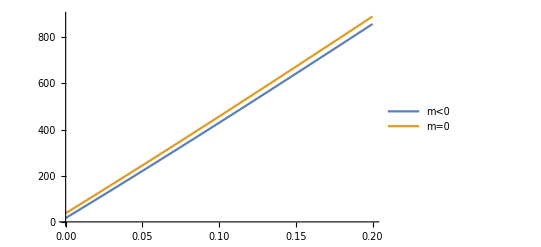

```mathematica
Plot[Evaluate[{Fbcmm1[n],FbcHalf[n]}/.{q->2,Γ->0.001}],{p,0,.2},PlotLegends->{"m<0","m=0","m>>0","m>0"}]
```

```mathematica
w000=w3test[1,1,1,q,Γ,p];
w001=w3test[1,1,-1,q,Γ,p];
w010=w3test[1,-1,1,q,Γ,p];
w100=w3test[-1,1,1,q,Γ,p];
w101=w3test[-1,1,-1,q,Γ,p];
w011=w3test[1,-1,-1,q,Γ,p];
w110=w3test[-1,-1,1,q,Γ,p];
w111=w3test[-1,-1,-1,q,Γ,p];

M={{1,1,1,1,1,1,1,1},{1,1,1,-1,1,-1,-1,-1},{1,1,-1,1,-1,-1,1,-1},{1,-1,1,1,-1,1,-1,-1},{1,1,-1,-1,-1,1,-1,1},{1,-1,1,-1,-1,-1,1,1},{1,-1,-1,1,1,-1,-1,1},{1,-1,-1,-1,1,1,1,-1}};
MI = Inverse[M];
v= MI.Log[{w000,w001,w010,w100,w101,w011,w110,w111}];
vLegend={"h0","h1","h2","h3","J12","J23","J31","J123"};
```

```mathematica
Collect[Series[v[[6]]/.q->2,{Γ,0,2},{p,0.16,2}],p]/.Γ->0 
Collect[Series[v[[5]]/.q->2,{Γ,0,2},{p,0.16,2}],p]/.Γ->0 
Collect[Series[v[[8]]/.q->2,{Γ,0,2},{p,0.16,2}],p]
Collect[Series[(v[[1]]+v[[2]]+v[[3]])/.q->2,{
Γ,0,2},{p,0.16,2}],p]/.Γ->0
```

1.99661-6.74717 p+9.5378 p^2

-1.54216+6.81362 p-10.2006 p^2

49.2581 Γ-3638.4 Γ^2+p^2 (1022.67 Γ-98924.6 Γ^2)+p (-429.721 Γ+37359.6 Γ^2)

-2.44423+2.56421 p-9.34545 p^2

```mathematica
Perhaps one needs to reverse this using the Virial expansion, i.e. writing p,Gamma in terms of J12, J23, J123 etc at different orders of p and Gamma.
```

```mathematica
Simplify[wdtest[1,1,q,0,p]-wdtest[-1,-1,q,0,p]]
Simplify[wdtest[1,-1,q,0,p]-wdtest[-1,1,q,0,p]]
Simplify[w3test[1,1,1,2,0,p]-w3test[-1,-1,-1,2,0,p]]
```

0

0

0

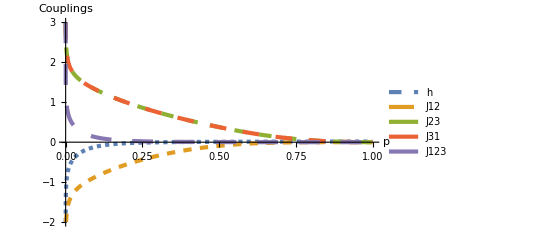

```mathematica
vNew = {v[[2]]+v[[3]]+v[[4]],v[[5]],v[[6]],v[[7]],v[[8]]};
vNewLegend={"h","J12","J23","J31","J123"};
dashThick=Transpose[{Table[AbsoluteDashing[i],{i,3,15,3}],
Table[AbsoluteThickness[3],{i,1,5}]}];
phaseDampGamma001q2 = Plot[Evaluate @Table[Indexed[vNew/.{q->2,Γ->0.01},i],{i,5}],{p,0,1},PlotLegends->LineLegend[Automatic,vNewLegend,Spacings->0.15],AxesLabel->{"p","Couplings"},LabelStyle->{FontSize->22},PlotStyle->dashThick, PlotRange-> {{0,1},{-2,3}}]
(*Export["/Users/cathy/Google Drive/Random circuits/Pics/phaseDamp_Gammma001_q2.png",Rasterize[phaseDampGamma001q2,ImageResolution->150]];*)
```

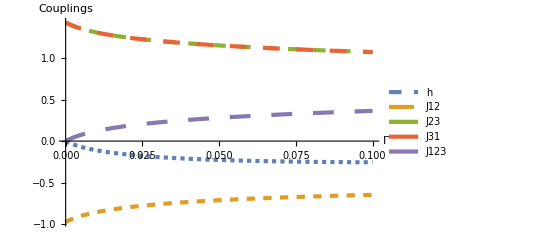

```mathematica
Plot[Evaluate @Table[Indexed[vNew/.{q->2,p->0.1},i],{i,5}],{Γ,0,0.1},PlotLegends->LineLegend[Automatic,vNewLegend,Spacings->0.15],AxesLabel->{"Γ","Couplings"},LabelStyle->{FontSize->22},PlotStyle->dashThick, PlotRange-> Automatic]
```

```mathematica
ResourceFunction["MaTeXInstall"][]
```

Paclet[MaTeX,1.7.9,<>]

```mathematica
Needs["MaTeX`"]
```

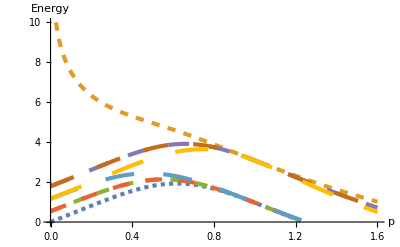

```mathematica
dashThick=Transpose[{Table[AbsoluteDashing[i],{i,3,25,3}],
Table[AbsoluteThickness[3],{i,1,8}]}];
wLegend=MaTeX[{"w^{(2)}(\\uparrow \\uparrow \\uparrow)","w^{(2)}(\\uparrow \\uparrow \\downarrow)","w^{(2)}(\\uparrow \\downarrow \\downarrow)","w^{(2)}(\\downarrow \\uparrow \\uparrow)","w^{(2)}(\\downarrow \\uparrow \\downarrow)","w^{(2)}(\\uparrow \\downarrow \\downarrow)","w^{(2)}(\\downarrow \\downarrow \\uparrow)","w^{(2)}(\\downarrow \\downarrow \\downarrow)"},Magnification->1.5];
boltzmann3 =Plot[Evaluate[-Log[{w000,w001,w010,w100,w101,w011,w110,w111}]/.{q->2,Γ->0.5}],{p,0,1.6},PlotLegends->LineLegend[Automatic,wLegend,Spacings->0.15],AxesLabel->{"p","Energy"},LabelStyle->{FontSize->22},PlotRange->{{0,1.6},{0,10}}, PlotStyle->dashThick]
(*Export["/Users/cathy/Google Drive/Random circuits/Pics/w3_math.png",Rasterize[boltzmann3,ImageResolution->150]]*)
```

```mathematica
Simplify[w101**2/(w000*w110)/.{q->2,Γ->0.001}]
```

(1.00176 (0.399467-1.59787 p+2.99547 p^2-2.7952 p^3+1.1976 p^4)**2)/(0.000534273-0.00427418 p+0.283129 p^2-1.63894 p^3+4.5104 p^4-7.19513 p^5+6.98095 p^6-3.89655 p^7+1. p^8)

```mathematica
max3Plaqs=Max[w110*w000^2,w111*w010*w100]
```

Max[(-1/60 (1-2 p+2 p^2)^2 (2+2 Γ^2)^2+1/15 (p^2 (1+(1-Γ)^2+Γ^2)+(1-p)^2 (1+2 (1-Γ)+(1-Γ)^2+Γ^2))^2) (1/15 (1-2 p+2 p^2) (2+2 Γ^2) (4-8 p+2 p^2 (3+Γ^2))-1/60 (p^2 (1+(1-Γ)^2+Γ^2)+(1-p)^2 (1+2 (1-Γ)+(1-Γ)^2+Γ^2)) (2-4 p+p^2 (4-2 (Γ-Γ^2))))^2,(1/15 (1-2 p+2 p^2)^2 (2+2 Γ^2)^2-1/60 (p^2 (1+(1-Γ)^2+Γ^2)+(1-p)^2 (1+2 (1-Γ)+(1-Γ)^2+Γ^2))^2) (1/15 (4-8 p+2 p^2 (3+Γ^2))^2-1/60 (2-4 p+p^2 (4-2 (Γ-Γ^2)))^2)^2]

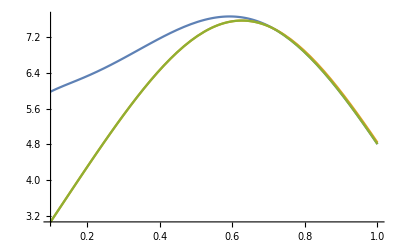

```mathematica
Plot[Evaluate[{-Log[w110*w000^2],-Log[w111*w010*w100],-Log[max3Plaqs]}/.{q->2,Γ->0.01}],{p,0.1,1}]
```

```mathematica
FortranForm[ (v[[2]]+v[[3]]+v[[4]])/.{Γ->g}]
```

-Log(-((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -            (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -               (1 - g)**2*(-2 + q)*(-1 + q)))**2/(q**2*(-1 + q**4))) + 
     -      ((1 - 2*p + 2*p**2)**2*(2*g**2 + q)**2)/(-1 + q**4))/8. - 
     -  (3*Log((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -           (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -              (1 - g)**2*(-2 + q)*(-1 + q)))**2/(-1 + q**4) - 
     -       ((1 - 2*p + 2*p**2)**2*(2*g**2 + q)**2)/(q**2*(-1 + q**4))))/8. + 
     -  Log(-(((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -            (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -               (1 - g)**2*(-2 + q)*(-1 + q)))*(q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q)))/
     -        (q**2*(-1 + q**4))) + ((1 - 2*p + 2*p**2)*(2*g**2 + q)*
     -        (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.)))/(-1 + q**4))/4. - 
     -  Log(((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -          (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -             (1 - g)**2*(-2 + q)*(-1 + q)))*(q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q)))/
     -      (-1 + q**4) - ((1 - 2*p + 2*p**2)*(2*g**2 + q)*
     -        (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.)))/(q**2*(-1 + q**4)))/4. + 
     -  (3*Log(-((q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q))**2/(q**2*(-1 + q**4))) + 
     -       (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.))**2/(-1 + q**4)))/8. + 
     -  Log((q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q))**2/(-1 + q**4) - 
     -     (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.))**2/(q**2*(-1 + q**4)))/8.

```mathematica
FortranForm[v[[5]]/.{Γ->g}]
```

Log(-((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -           (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -              (1 - g)**2*(-2 + q)*(-1 + q)))**2/(q**2*(-1 + q**4))) + 
     -     ((1 - 2*p + 2*p**2)**2*(2*g**2 + q)**2)/(-1 + q**4))/8. + 
     -  Log((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -         (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -            (1 - g)**2*(-2 + q)*(-1 + q)))**2/(-1 + q**4) - 
     -     ((1 - 2*p + 2*p**2)**2*(2*g**2 + q)**2)/(q**2*(-1 + q**4)))/8. - 
     -  Log(-(((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -            (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -               (1 - g)**2*(-2 + q)*(-1 + q)))*(q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q)))/
     -        (q**2*(-1 + q**4))) + ((1 - 2*p + 2*p**2)*(2*g**2 + q)*
     -        (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.)))/(-1 + q**4))/4. - 
     -  Log(((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -          (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -             (1 - g)**2*(-2 + q)*(-1 + q)))*(q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q)))/
     -      (-1 + q**4) - ((1 - 2*p + 2*p**2)*(2*g**2 + q)*
     -        (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.)))/(q**2*(-1 + q**4)))/4. + 
     -  Log(-((q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q))**2/(q**2*(-1 + q**4))) + 
     -     (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.))**2/(-1 + q**4))/8. + 
     -  Log((q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q))**2/(-1 + q**4) - 
     -     (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.))**2/(q**2*(-1 + q**4)))/8.

```mathematica
FortranForm[v[[8]]/.{Γ->g}]
```

-Log(-((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -            (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -               (1 - g)**2*(-2 + q)*(-1 + q)))**2/(q**2*(-1 + q**4))) + 
     -      ((1 - 2*p + 2*p**2)**2*(2*g**2 + q)**2)/(-1 + q**4))/8. + 
     -  Log((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -         (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -            (1 - g)**2*(-2 + q)*(-1 + q)))**2/(-1 + q**4) - 
     -     ((1 - 2*p + 2*p**2)**2*(2*g**2 + q)**2)/(q**2*(-1 + q**4)))/8. + 
     -  Log(-(((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -            (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -               (1 - g)**2*(-2 + q)*(-1 + q)))*(q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q)))/
     -        (q**2*(-1 + q**4))) + ((1 - 2*p + 2*p**2)*(2*g**2 + q)*
     -        (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.)))/(-1 + q**4))/4. - 
     -  Log(((p**2*(1 + ((1 - g)**2 + g**2)*(-1 + q)) + 
     -          (1 - p)**2*(1 + 2*(1 - g)*(-1 + q) + ((1 - g)**2 + g**2)*(-1 + q) + 
     -             (1 - g)**2*(-2 + q)*(-1 + q)))*(q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q)))/
     -      (-1 + q**4) - ((1 - 2*p + 2*p**2)*(2*g**2 + q)*
     -        (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.)))/(q**2*(-1 + q**4)))/4. - 
     -  Log(-((q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q))**2/(q**2*(-1 + q**4))) + 
     -     (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.))**2/(-1 + q**4))/8. + 
     -  Log((q - 2*p*q + p**2*(-2*(g - g**2)*(-1 + q) + 2*q))**2/(-1 + q**4) - 
     -     (q**2 - 2*p*q**2 + 2*p**2*(g**2 + (q*(1 + q))/2.))**2/(q**2*(-1 + q**4)))/8.

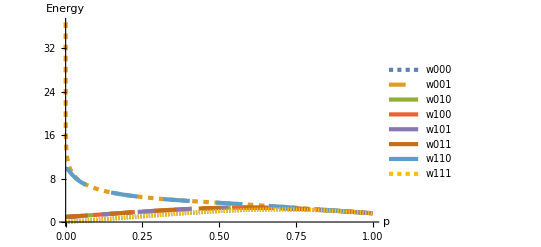

```mathematica
dashThick=Transpose[{Table[AbsoluteDashing[i],{i,1,19,3}],
Table[AbsoluteThickness[3],{i,1,7}]}];
BoltzmannW = {"w000","w001","w010","w100","w101","w011","w110","w111"};
p4=Plot[Evaluate @ Table[Indexed[-Log[{w000,w001,w010,w100,w101,w011,w110,w111}]/.{q->2,Γ->0.0001},i],{i,8}],{p,0,1},AxesLabel->{"p","Energy"},PlotLegends->LineLegend[Automatic,BoltzmannW,Spacings->0.15],LabelStyle->{FontSize->22},PlotStyle->dashThick,PlotRange->Full]
(*Export["/Users/cathy/Google Drive/Random circuits/Pics/phaseDamp_w3_Gamma01.png",Rasterize[p4,ImageResolution->150]]*)
```

```mathematica
Export["/Users/cathy/Google Drive/Random circuits/Pics/phaseDamp_Gamma001_q2.png",Rasterize[phaseDampGamma001q2,ImageResolution->150]];
```

```mathematica
FullSimplify[v[[5]]]
```

1/8 (Log[1/(-1+q^4)((1+2 (-1+p) p)^2 (q+2 Γ^2)^2-1/q^2(q (p^2+(-1+p)^2 q)-2 (-1+q) (p^2+(-1+p)^2 q) Γ+(-1+q) (q-2 p q+p^2 (2+q)) Γ^2)^2)]+Log[(-((q (p^2+(-1+p)^2 q)+2 p^2 Γ^2)^2)/q^2+(q-2 p q+2 p^2 (q+(-1+q) (-1+Γ) Γ))^2)/(-1+q^4)]-2 Log[1/(-1+q^4)(-1/q^2(q (p^2+(-1+p)^2 q)-2 (-1+q) (p^2+(-1+p)^2 q) Γ+(-1+q) (q-2 p q+p^2 (2+q)) Γ^2) (q-2 p^2 (-1+Γ) Γ+2 p q (-1+p+p (-1+Γ) Γ))+(1+2 (-1+p) p) (q+2 Γ^2) (q^2-2 p q^2+p^2 (q+q^2+2 Γ^2)))]+Log[(-((q-2 p q+2 p^2 (q+(-1+q) (-1+Γ) Γ))^2)/q^2+(q^2-2 p q^2+p^2 (q+q^2+2 Γ^2))^2)/(-1+q^4)]-2 Log[1/(-1+q^4)(-((1+2 (-1+p) p) (q+2 Γ^2) (q (p^2+(-1+p)^2 q)+2 p^2 Γ^2))/q^2+(q-2 p q+2 p^2 (q+(-1+q) (-1+Γ) Γ)) ((-1+p)^2 q (q (-1+Γ)^2-(-2+Γ) Γ)+p^2 (1+(-1+q) (1+2 (-1+Γ) Γ))))]+Log[1/(-1+q^4)(-((1+2 (-1+p) p)^2 (q+2 Γ^2)^2)/q^2+((-1+p)^2 q (q (-1+Γ)^2-(-2+Γ) Γ)+p^2 (1+(-1+q) (1+2 (-1+Γ) Γ)))^2)])

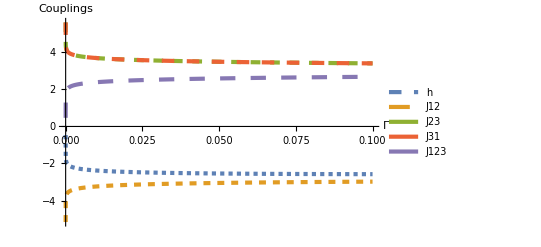

```mathematica
dashThick=Transpose[{Table[AbsoluteDashing[i],{i,3,15,2}],
Table[AbsoluteThickness[3],{i,1,7}]}];
phaseDampp01q2 = Plot[Evaluate @ Table[Indexed[vNew/.{q->2,p->0.00001},i],{i,5}],{Γ,0,0.1},PlotLegends->LineLegend[Automatic,vNewLegend,Spacings->0.15],AxesLabel->{"Γ","Couplings"},LabelStyle->{FontSize->22},PlotStyle->dashThick, PlotRange-> Automatic]
(*Export["/Users/cathy/Google Drive/Random circuits/Pics/phaseDamp_p01_q2.png",Rasterize[phaseDampp01q2,ImageResolution->150]];*)
```

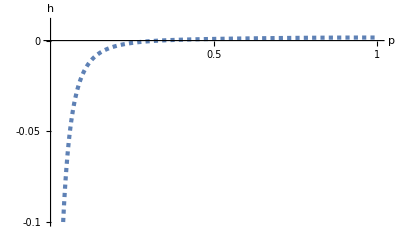

```mathematica
exfield= Plot[Evaluate @ Table[Indexed[vNew/.{q->2,Γ->0.001},i],{i,1,1}],{p,0,1},AxesLabel->{Style["p",30],Style["h",30]},PlotStyle->{ColorData[97][1],dashThick[[1]]}, PlotRange-> {{0,1},{-0.1,0.01}},Ticks-> {{0.5,1},{0,-0.05,-0.1}},TicksStyle->{{20},{20}}]
```

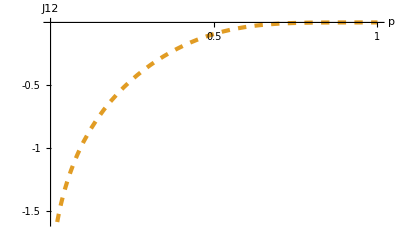

```mathematica
horJ= Plot[Evaluate @ Table[Indexed[vNew/.{q->2,Γ->0.001},i],{i,2,2}],{p,0,1},AxesLabel->{Style["p",30],Style["J12",28]},PlotStyle->{ColorData[97][2],dashThick[[2]]},LabelStyle->{FontSize->22}, PlotRange-> Automatic,Ticks-> {{0.5,1},{-1.5,-1,-0.5}},TicksStyle->{{20},{20}}]
```

```mathematica
n=32
Plot3D[{-(n/2(Log[w100]+Log[w011])+(n/2-1)n/4*Log[w111]+((n-1)^2-n-(n/2-1)n/4) Log[w000])/.{q->100},-(n/2(Log[w100]+Log[w011])+(n/2-1)n/4*Log[w000]+((n-1)^2-n-(n/2-1)n/4) Log[w111])/.{q->100}, -((n-2)*(n-1)/2*(Log[w000]+Log[w111])+(n-1)(Log[w011]+Log[w100]))/.{q->100}},{p,0,0.5},{Γ,0,0.001},PlotLegends->{"wall encases -","wall encases +","half+ half-"}]
Plot3D[ (-n/2(Log[w100]+Log[w011])+(n/2-1)n/4*Log[w111]+((n-1)^2-n-(n/2-1)n/4) Log[w000])+(n/2(Log[w100]+Log[w011])+(n/2-1)n/4*Log[w000]+((n-1)^2-n-(n/2-1)n/4) Log[w111])/.{q->2},{p,0,0.5},{Γ,0,0.001},PlotLegends->{"vertical dom","horizontal dom"}]
```

32

-Graphics3D-

-Graphics3D-

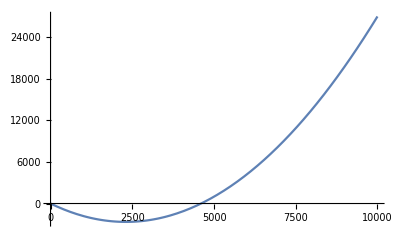

```mathematica
Plot[n^2*0.001/2-n/2 Log[100],{n,0,10000}]
```

```mathematica
n=100
Plot3D[{(n-1)^2*Log[w000]+(n-1)/2*Log[w110]/.{q->2},
(n-1)^2*Log[w111]+(n-1)/2*Log[w001]/.{q->2},(((n-1)^2-2(n-1))/2(Log[w000]+Log[w111])+ 2(n-1)*( Log[w101]+Log[w100]))+n Log[2]/.{q->2}},{p,0,0.5},{Γ,0,0.001},PlotLegends->{"+","-","domWall"},AxesLabel->Automatic]
```

100

-Graphics3D-

```mathematica
n=100
Plot3D[{-((n-1)(n-2)+n/2)*Log[w000]-n/2*Log[w110]-(-((n-1)(n-2)+n/2)*Log[w111]-n/2*Log[w001])/.{q->2}},{p,0,0.6},{Γ,0,0.0001},PlotLegends->Automatic,AxesLabel->Automatic]
Plot3D[{-((n-1)(n-2)+n/2)*Log[w000]-n/2*Log[w110]-n/2*Log[w111]/.{q->2},-((n-1)(n-2)+n/2)*Log[w111]-n/2*Log[w000]-n/2*Log[w001]/.{q->2}},{p,0,0.6},{Γ,0,0.0001},PlotLegends->Automatic,AxesLabel->Automatic]
```

100

-Graphics3D-

-Graphics3D-